```mathematica
SetDirectory["C:\\Users\\sojoodif\\surfdrive\\sync\\MyPhD\\experiments\\friction\\20180503"]
```

C:\Users\sojoodif\surfdrive\sync\MyPhD\experiments\friction\20180503

```mathematica
s=Import["analysis.xlsx"]
```

{{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,15.2848,0.197084,0.0519472,1.10845,0.188964,0.169225,1.10822,0.186019},{53.,36.8176,0.247168,0.0668231,1.1486,0.155977,0.190487,1.14562,0.19563},{65.,14.2594,0.266691,0.0748634,1.1233,0.232937,0.224971,1.09408,0.237601},{77.,26.2256,0.334639,0.0757782,1.55337,0.239123,0.244285,1.38127,0.35947},{89.,19.4298,0.368608,0.100657,1.08529,0.206955,0.291185,1.08656,0.218317},{136.,10.2703,0.499416,0.081453,1.60402,0.157233,0.413429,1.59796,0.15809},{184.,21.5883,0.651468,0.115851,2.02076,0.346475,0.546717,2.1752,0.309378},{232.,43.7341,0.767838,0.131922,1.76534,0.285033,0.637307,1.73182,0.313921}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,32.2667,0.182641,0.0540465,0.82242,0.18629,0.147084,0.815867,0.187156},{53.,29.7547,0.22338,0.0712302,0.847728,0.146523,0.176005,0.827964,0.153299},{65.,53.8142,0.242054,0.0780273,0.838002,0.153819,0.199523,0.837908,0.151823},{77.,9.63776,0.297259,0.0915199,1.0324,0.177729,0.239157,1.03583,0.173153},{89.,38.4704,0.335477,0.110405,0.822395,0.155328,0.263541,0.814518,0.157581},{136.,9.49004,0.45694,0.0890582,1.21029,0.168666,0.343452,1.20025,0.186963},{184.,27.1638,0.547828,0.115922,1.42392,0.199835,0.470145,1.42499,0.199484},{232.,12.0212,0.702426,0.145854,1.35828,0.186059,0.57283,1.34329,0.195046}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,30.8291,0.179243,0.0597455,0.668797,0.130875,0.138131,0.663865,0.133011},{53.,15.2751,0.218283,0.0790037,0.763367,0.129346,0.176703,0.762413,0.128565},{65.,19.5911,0.236957,0.0862031,0.757887,0.168038,0.194137,0.762249,0.166022},{77.,51.4024,0.293011,0.100751,0.85261,0.136173,0.227983,0.841688,0.143909},{89.,59.2082,0.307442,0.105094,0.742288,0.164723,0.238547,0.758399,0.157616},{136.,9.50115,0.471382,0.101771,1.06492,0.186478,0.34446,1.09009,0.168147},{184.,10.9101,0.546978,0.121354,1.10517,0.182524,0.386818,1.07974,0.200659},{232.,11.8594,0.733858,0.156052,1.14248,0.156728,0.484028,1.13974,0.166558}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,32.5419,0.203031,0.0787551,0.621641,0.128184,0.139964,0.623644,0.128274},{53.,23.5836,0.214035,0.0817424,0.693307,0.122115,0.154668,0.692008,0.119937},{65.,29.4502,0.221665,0.103497,0.645829,0.102261,0.185357,0.643013,0.101658},{77.,35.5217,0.253083,0.108806,0.773547,0.122251,0.210894,0.767177,0.120037},{89.,8.46711,0.274311,0.114694,0.750537,0.104953,0.226902,0.751918,0.0991229},{136.,10.4366,0.460338,0.127934,0.903513,0.132702,0.295868,0.888814,0.141899},{184.,10.3838,0.520643,0.142218,0.964744,0.112136,0.355854,0.954808,0.122256},{232.,12.2002,0.703276,0.189381,1.06666,0.100921,0.49779,1.06583,0.10148}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,5.88792,0.180092,0.0835233,0.802819,0.202349,0.135147,0.791238,0.185527},{53.,11.3501,0.199593,0.0852425,0.852424,0.181338,0.152706,0.848377,0.187817},{65.,48.6757,0.228461,0.10588,0.779547,0.106853,0.183423,0.765136,0.105767},{77.,9.95586,0.242889,0.122863,0.775366,0.106709,0.210931,0.77281,0.105389},{89.,54.3255,0.255621,0.124444,0.788989,0.108152,0.219104,0.793571,0.107455},{136.,10.2325,0.480726,0.130359,0.844666,0.121125,0.281606,0.843761,0.113822},{184.,9.94997,0.537634,0.154519,0.914581,0.100622,0.330183,0.923656,0.100447},{232.,11.2509,0.651456,0.192245,1.02183,0.102016,0.437699,1.0366,0.113433}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,6.38319,0.163101,0.0787656,1.08889,0.262108,0.125352,1.13638,0.333943},{53.,18.3348,0.192796,0.0918003,1.21903,0.353271,0.149015,1.26045,0.353027},{65.,21.7997,0.208922,0.105523,1.12314,0.334969,0.173376,1.17427,0.29132},{77.,8.24146,0.247137,0.123152,0.952197,0.217392,0.208133,1.06971,0.321095},{89.,19.0419,0.245427,0.127615,0.906953,0.132613,0.216463,1.0124,0.226143},{136.,9.8095,0.454391,0.137452,1.00672,0.0929728,0.289706,1.00675,0.0968553},{184.,10.9333,0.552925,0.173119,1.07104,0.139492,0.35313,1.05845,0.119022},{232.,11.6345,0.624272,0.202882,1.01305,0.108597,0.408745,1.01808,0.136054}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,5.87659,0.163101,0.0814238,1.84518,0.518537,0.107742,2.09201,0.663422},{53.,6.20148,0.16561,0.0928948,1.78146,0.521539,0.132682,1.9084,0.576751},{65.,15.6009,0.197028,0.121115,1.93181,0.495693,0.164189,1.80943,0.566362},{77.,8.4141,0.230995,0.127564,1.85358,0.483293,0.193307,2.02722,0.486584},{89.,9.0018,0.272612,0.135441,1.58109,0.323643,0.211556,2.17011,0.550227},{136.,9.61307,0.420411,0.131669,1.90414,0.737248,0.255027,1.83198,0.614847},{184.,10.8515,0.496857,0.175292,1.41177,0.405533,0.332278,1.50667,0.489101},{232.,11.9501,0.742353,0.217358,1.34855,0.308679,0.393085,1.39681,0.397116}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,6.10112,0.169897,0.0912339,2.06644,0.418173,0.115694,2.54002,0.874968},{53.,5.53403,0.159664,0.0968909,2.58527,0.614703,0.128109,2.52702,0.742186},{65.,38.4679,0.170692,0.119889,2.43998,0.612041,0.152946,2.28898,0.449412},{77.,10.8186,0.235243,0.124464,3.32443,0.790665,0.195995,3.67965,0.973847},{89.,10.2683,0.227587,0.13335,3.51435,1.12358,0.213258,3.22666,0.835444},{136.,9.81879,0.430605,0.152413,2.4864,0.373502,0.267073,3.33433,1.04682},{184.,10.6013,0.542731,0.166747,2.75976,0.642213,0.31537,4.02427,1.75228},{232.,11.8017,0.646359,0.206136,2.50184,0.661464,0.380039,3.5014,1.30421}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,5.13346,0.169897,0.0831835,3.87551,1.12047,0.102143,4.53326,1.26656},{53.,12.4832,0.148619,0.100195,4.59095,1.46843,0.125141,4.46749,1.64136},{65.,23.3824,0.159648,0.120965,3.85193,1.18961,0.14514,4.44438,1.82579},{77.,33.9079,0.198713,0.131478,4.17908,1.49341,0.169149,3.94575,1.07432},{89.,7.6832,0.23863,0.138154,5.462,1.9338,0.193545,4.21331,1.32948},{136.,9.40712,0.377935,0.155927,5.64514,1.66029,0.2991,5.59815,2.0383},{184.,11.1822,0.507051,0.168636,4.12717,0.902739,0.306821,4.77998,1.22408},{232.,11.8821,0.69563,0.216131,4.99994,0.889351,0.419435,7.04506,2.35642}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,6.54971,0.141861,0.081737,4.56535,1.3014,0.102356,5.81184,1.49667},{53.,6.21712,0.174106,0.0996637,6.94801,2.0146,0.116525,5.48131,1.58693},{65.,6.74931,0.180037,0.114622,5.98153,2.02762,0.139542,6.10111,1.67526},{77.,6.78284,0.157935,0.137624,4.53316,1.26074,0.152298,5.06758,1.54665},{89.,6.21734,0.194455,0.137348,5.01671,1.24833,0.167755,6.59033,1.81763},{136.,9.98395,0.417862,0.147857,9.70811,2.77498,0.219439,7.46386,2.89162},{184.,10.4837,0.498556,0.18452,9.48612,2.89699,0.273624,6.42369,1.80967},{232.,12.2163,0.659102,0.229737,8.10707,2.40813,0.314485,5.27408,1.77124}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,5.82697,0.172446,0.0817109,5.98299,1.72469,0.0952556,7.042,2.14332},{53.,5.91035,0.146071,0.0953098,7.32229,1.82225,0.112695,7.00623,1.71935},{65.,5.9108,0.186833,0.114027,5.95772,1.94072,0.129772,5.7291,1.62521},{77.,5.78574,0.173227,0.123833,6.33315,2.28527,0.13967,5.04168,0.552389},{89.,7.0776,0.253922,0.128723,7.46791,2.63527,0.147837,6.25017,1.97871},{136.,9.78594,0.400872,0.157697,7.47324,1.63992,0.225264,7.79798,2.53118},{184.,10.0777,0.494309,0.175848,7.50957,2.80406,0.237756,5.83335,1.58336},{232.,12.0767,0.598787,0.251126,5.66662,1.49945,0.344177,7.75661,3.34064}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,5.02902,0.152906,0.0749567,8.84026,2.12528,0.0919483,11.2001,3.26647},{53.,4.91211,0.140973,0.0959469,9.60748,2.71901,0.10602,7.73334,2.89527},{65.,5.846,0.163896,0.109312,14.9947,4.29031,0.126516,16.3334,4.66644},{77.,6.60454,0.191067,0.124124,11.8795,5.64004,0.141964,9.42665,2.165},{89.,7.94624,0.229286,0.134138,11.9607,4.45445,0.162173,23.0997,0.23268},{136.,9.87112,0.433153,0.154002,12.0541,2.39504,0.195572,7.93325,2.33357},{184.,10.2789,0.47392,0.186219,9.72442,3.0353,0.22388,12.7556,7.0525},{232.,11.6798,0.59284,0.229737,8.60172,2.55503,0.279797,11.5498,5.25009}},{{,static_strain(mm),static_force,min_mean,min_del,min_del_mad,max_mean,max_del,max_del_mad},{41.,5.44023,0.155455,0.0743195,10.0063,2.59381,0.0900368,12.2993,4.1994},{53.,5.28934,0.133327,0.0894903,11.7377,3.28515,0.0999823,11.5497,2.84999},{65.,6.1888,0.169842,0.108335,12.0373,3.15026,0.121843,11.5496,3.74984},{77.,7.16347,0.195315,0.122595,6.37507,2.09993,0.136697,12.9,3.29949},{89.,8.28835,0.232684,0.152658,11.8573,3.42882,0.172792,10.9312,1.66881},{136.,10.1632,0.42126,0.145677,11.6472,4.10761,0.184245,21.8996,3.89983},{184.,10.3875,0.479017,0.176591,14.8967,4.25179,0.229685,20.1001,0.301215},{232.,12.1875,0.591991,0.203766,19.8626,2.71679,0.276824,40.1995,0.}},{{,static_force_a,static_force_b,static_strain_a,static_strain_b,kinetic_max_mean_a,kinetic_max_mean_b,kinetic_min_mean_a,kinetic_min_mean_b,kinetic_del_avg,kintetic_del_mad,mad/avg},{10.,0.305334,0.0882512,0.0675486,16.0462,0.259979,0.0601133,0.0364937,0.0481657,1.42062,0.236945,0.16679},{30.,0.269397,0.0837858,-0.112479,38.9079,0.224899,0.0596055,0.0385617,0.0530378,1.041,0.173672,0.166832},{50.,0.287002,0.0647462,-0.130052,40.3291,0.176924,0.0835828,0.0404365,0.0577605,0.887231,0.157461,0.177474},{100.,0.272256,0.0635084,-0.112755,32.6839,0.178209,0.066762,0.051782,0.062691,0.800437,0.116262,0.145248},{150.,0.266836,0.0600983,-0.0698606,27.862,0.150219,0.082301,0.0519,0.0690701,0.847211,0.128051,0.151145},{200.,0.265618,0.0504701,-0.018866,15.3405,0.149758,0.0794375,0.0605568,0.0649144,1.06984,0.21993,0.205572},{300.,0.301327,0.0120673,0.0187795,7.62998,0.145837,0.0668966,0.0622298,0.0684214,1.77501,0.508661,0.286567},{400.,0.281844,0.0197466,-0.0160047,14.681,0.138195,0.0724429,0.0554686,0.0767381,2.92505,0.825968,0.282377},{600.,0.294567,-0.00476792,-0.0255655,17.1853,0.162455,0.0453514,0.0599896,0.0748198,4.73495,1.4634,0.309064},{800.,0.287574,-0.00627337,0.0333067,4.49879,0.113649,0.0635324,0.0689388,0.0675002,6.40999,1.90803,0.297665},{1000.,0.254162,0.029977,0.035352,3.93102,0.123287,0.0464677,0.078741,0.0563545,6.63566,1.98911,0.299761},{1400.,0.257872,0.0199337,0.0365232,3.76711,0.0941635,0.0647183,0.0742789,0.0586734,11.7309,3.44228,0.293436},{1800.,0.257077,0.0208958,0.0361471,4.17591,0.0954254,0.0613906,0.0617933,0.0677252,14.9906,2.85017,0.190131},{,,,,,,,,,,,},{,0.27699,0.0386492,-0.0198405,17.4645,0.154846,0.0655848,0.0570131,0.0635286,4.25142,1.07846,0.22862},{,0.0531595,0.712385,-2.72567,0.615973,0.226762,0.135853,0.181973,0.107738,0.841165,0.893114,0.267255}}}

```mathematica
s[[1,All, 1]]//Grid
```

Grid[{,41.,53.,65.,77.,89.,136.,184.,232.}]

```mathematica
data=Transpose@{s[[1,2;;, 1]],s[[1,2;;, 3]]}
```

{{41.,0.197084},{53.,0.247168},{65.,0.266691},{77.,0.334639},{89.,0.368608},{136.,0.499416},{184.,0.651468},{232.,0.767838}}

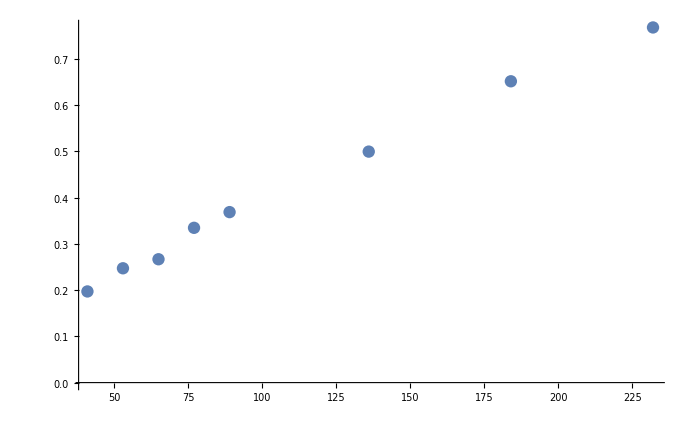

```mathematica
ListPlot[data]
```

```mathematica
FindFit[data,a*F^(2/3)+b*F,{a,b},F]
```

{a→0.0121015,b→0.00136286}

```mathematica
For[i=1,i<14,i++,
data=Transpose@{s[[i,2;;, 1]],s[[i,2;;, 3]]};
Print[FindFit[data,a*F^(2/3)+b*F,{a,b},F]]
]
```

{a→0.0121015,b→0.00136286}[1]

{a→0.0113152,b→0.00112502}[1]

{a→0.00854245,b→0.00167982}[1]

{a→0.00793512,b→0.00163882}[1]

{a→0.00814897,b→0.00152295}[1]

{a→0.00702748,b→0.00165242}[1]

{a→0.000898171,b→0.00287244}[1]

{a→0.00248805,b→0.00244017}[1]

{a→-0.00160922,b→0.00315425}[1]

{a→-0.001493,b→0.00305393}[1]

{a→0.0038229,b→0.00199192}[1]

{a→0.00281766,b→0.00214545}[1]

{a→0.00291794,b→0.00212568}[1]